## Resolución del sistema

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.1; Ω = 0.2;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + (I Ω)/2(1 + x[t]^2)== 0 ,y'[t] == I/2(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ (I Ω)/2 == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10];
```

### Probabilidades conjuntas

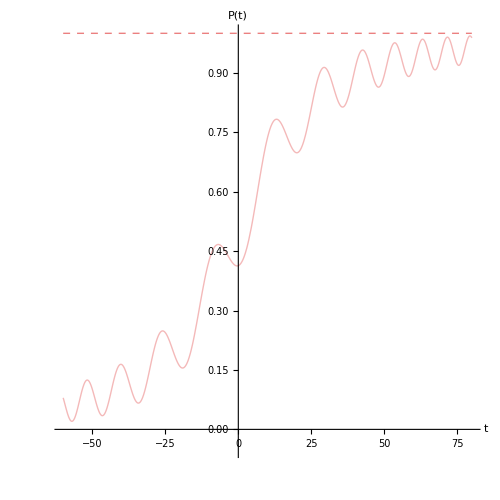

```mathematica
P1= Plot[{ (Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]],1-Exp[-π(Ω^2/(2(β^2)))]}, {t, -60, 80},PlotRange->{-0.05,1.0}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[RGBColor[0.92,0.5,0.5],Thickness[0.002], Opacity[0.55]], Directive[RGBColor[0.92,0.5,0.5],Thickness[0.002], Dashed]},AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P(t)",16, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500]
```

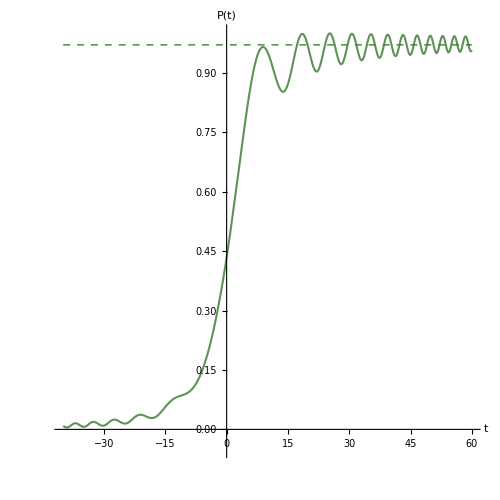

```mathematica
P2= Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]],1-Exp[-π(Ω^2/(2(β^2)))]}, {t, -40, 60}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[RGBColor[0.25,0.5,0.21],Thickness[0.003], Opacity[0.85]], Directive[RGBColor[0.25,0.5,0.21],Thickness[0.002], Dashed]},AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P(t)",16, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,PlotRange->{-0.05,1.0}]
```

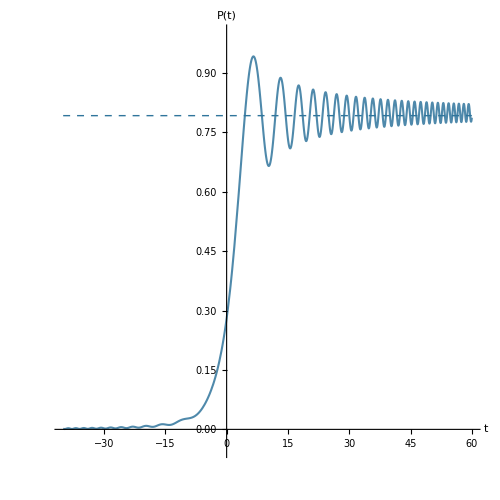

```mathematica
P3=  Plot[{ (Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]],1-Exp[-π(Ω^2/(2(β^2)))]}, {t, -40, 60}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[RGBColor[0.19,0.46,0.61],Thickness[0.003], Opacity[0.85]], Directive[RGBColor[0.19,0.46,0.61],Thickness[0.002], Dashed]},AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P(t)",16, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,PlotRange->{-0.05,1.0}]
```

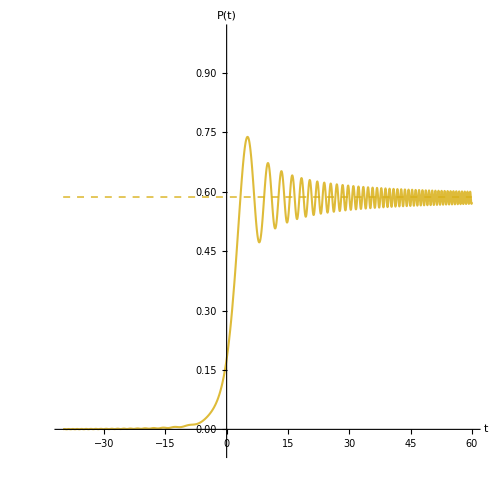

```mathematica
P4=  Plot[{ (Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]],1-Exp[-π(Ω^2/(2(β^2)))]}, {t, -40, 60}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[RGBColor[0.85,0.69,0.09],Thickness[0.003], Opacity[0.85]], Directive[RGBColor[0.85,0.69,0.09],Thickness[0.002], Dashed]},AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P(t)",16, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,PlotRange->{-0.05,1.0}]
```

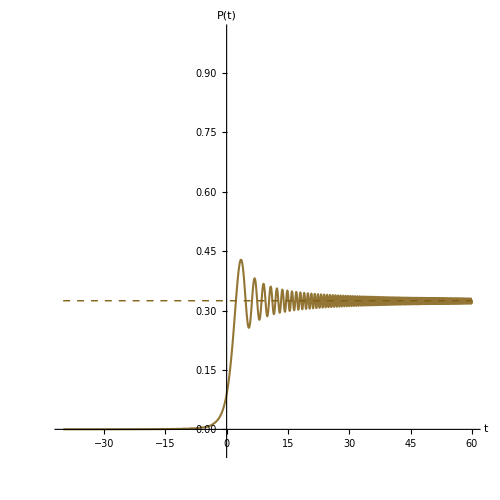

```mathematica
P5=  Plot[{ (Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]],1-Exp[-π(Ω^2/(2(β^2)))]}, {t, -40, 60}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[RGBColor[0.5,0.37,0.07],Thickness[0.003], Opacity[0.85]], Directive[RGBColor[0.5,0.37,0.07],Thickness[0.002], Dashed]},AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P(t)",16, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,PlotRange->{-0.05,1.0}]
```

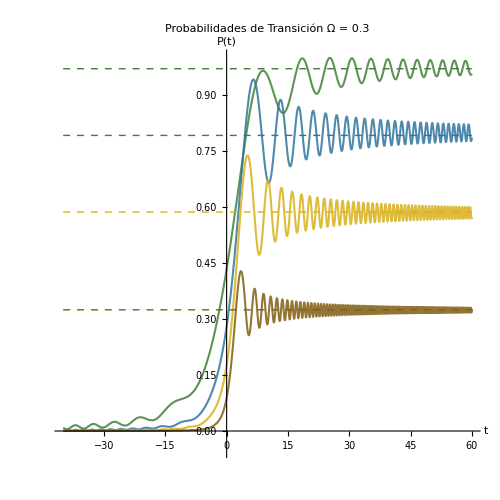

```mathematica
Labeled[Show[{P2,P3,P4,P5}, PlotLabel->Style["Probabilidades de Transición  Ω = 0.3", 18, FontFamily->"Times New Roman", Black]], LineLegend[{ RGBColor[0.25,0.5,0.21],RGBColor[0.19,0.46,0.61],RGBColor[0.85,0.69,0.09],RGBColor[0.5,0.37,0.07], Directive[Black, Dashed]},{Style["β=0.2, δ=1.125"], Style["β=0.3, δ=0.5"],Style["β=0.4, δ=0.28"],Style["β=0.6, δ=0.125"],Style["Fórmula LZSM"]}, LegendLayout->"Column"], Right]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/probabilidades_beta",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/probabilidades_beta

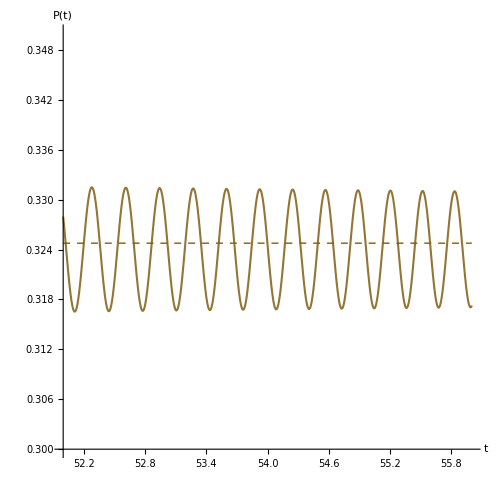

```mathematica
Plot[{ (Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]],1-Exp[-π(Ω^2/(2(β^2)))]}, {t, 52, 56},PlotStyle->{Directive[RGBColor[0.5,0.37,0.07],Thickness[0.003], Opacity[0.85]], Directive[RGBColor[0.5,0.37,0.07],Thickness[0.002], Dashed]},AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P(t)",16, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,PlotRange->{0.3,0.35}]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/probabilidades_beta_zoom1",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/probabilidades_beta_zoom1

### Niveles de energia conjuntos

```mathematica
Emas[T_]:= 1/2 Sqrt[Ω^2 +del[T]^2]
```

```mathematica
PP1 = Plot[{Emas[t], 1/2 del[t],-Emas[t],-1/2 del[t]}, {t, -3, 3}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003], RGBColor[0.92,0.5,0.5]], Directive[Dashed, Black, Thickness[0.002]],Directive[Thickness[0.003], RGBColor[0.92,0.5,0.5]], Directive[Dashed, Black,  Thickness[0.002]] },AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500, PlotLegends-> {"Ω = 0.2","Ω = 0"}];
```

```mathematica
PP2 = Plot[{Emas[t],-Emas[t]}, {t, -3, 3}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003],RGBColor[1,0.69,0.26]], Directive[Thickness[0.003], RGBColor[1,0.69,0.26]] },AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500, PlotLegends-> {"Ω = 0.4"}];
```

```mathematica
PP3 = Plot[{Emas[t],-Emas[t]}, {t, -3, 3}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003],RGBColor[0.25,0.5,0.21]], Directive[Thickness[0.003], RGBColor[0.25,0.5,0.21]] },AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500, PlotLegends-> {"Ω = 0.6"}];
```

```mathematica
PP4 = Plot[{Emas[t],-Emas[t]}, {t, -3, 3}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003],RGBColor[0.14,0.74,0.5]], Directive[Thickness[0.003], RGBColor[0.14,0.74,0.5]] },AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500, PlotLegends-> {"Ω = 0.8"}];
```

```mathematica
PP5 = Plot[{Emas[t],-Emas[t]}, {t, -3, 3}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003],RGBColor[0.19,0.46,0.61]], Directive[Thickness[0.003], RGBColor[0.19,0.46,0.61]] },AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500, PlotLegends-> {"Ω = 1.0"}];
```

```mathematica
PP6 = Plot[{Emas[t],-Emas[t]}, {t, -3, 3}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003],RGBColor[0.09,0.51,0.79]], Directive[Thickness[0.003], RGBColor[0.09,0.51,0.79]] },AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500, PlotLegends-> {"Ω = 1.2"}];
```

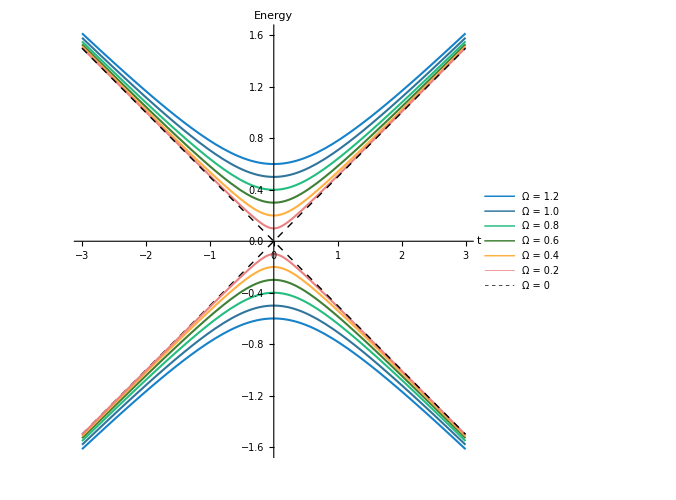

```mathematica
Show[PP6,PP5,PP4,PP3,PP2, PP1]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/escalado/energy_levels_varOmega1",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/escalado/energy_levels_varOmega1

## Probabilidades de Transición

Valor limite/estacionario esperado (t →  ∞)

```mathematica
Exp[1-π(Ω^2/(2(β^2)))]
```

0.761591

TRANSICIÓN DEL ESTADO BASE

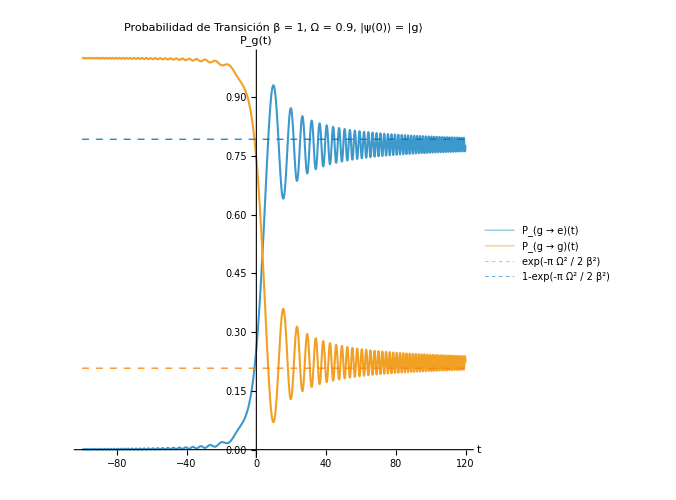

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -100, 120}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 1, Ω = 0.9, |ψ(0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/escalado/lineal/interaccion_debil/beta1/omega09/prob_base",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/escalado/lineal/interaccion_debil/beta1/omega09/prob_base

TRANSICIÓN DEL ESTADO EXCITADO

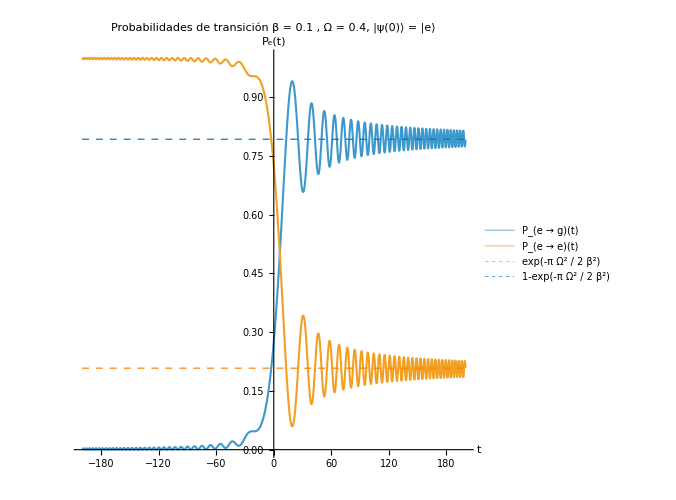

```mathematica
Plot[{(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2, Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -200, 200},
PlotLabel->Style["Probabilidades de transición  β = 0.1 , Ω = 0.4, |ψ(0)⟩ = |e⟩ ", 18, FontFamily->"Times New Roman", Black],PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},
PlotLegends-> {"P_(e  → g)(t)", "P_(e → e)(t)", "exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1,ImageSize->500,AxesLabel-> {Style["t",14,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",13,FontFamily->"Times New Roman",GrayLevel[0.26]]}]
```

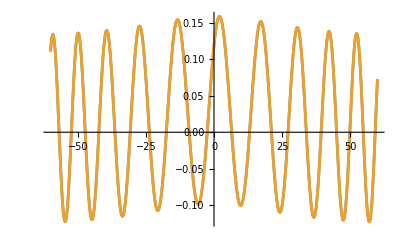

```mathematica
Plot[{Im[-alphaMenos[t] Exp[-2 alphaZ[t]]],-Im[alphaMenos[t] Exp[-2 alphaZ[t]] alphaMas[t]^2 + alphaMas[t]]}, {t, -60, 60}]
```

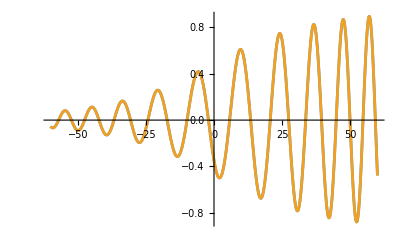

```mathematica
Plot[{Im[-Exp[-2 alphaZ[t]] alphaMenos[t] ^2],-Im[-Exp[-2 alphaZ[t]] alphaMas[t] ^2]}, {t, -60, 60}]
```

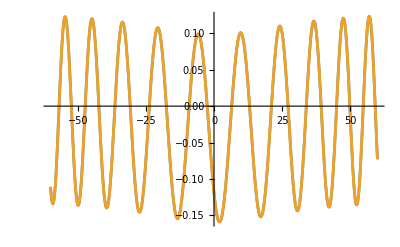

```mathematica
Plot[{Im[Exp[-2 alphaZ[t]] alphaMenos[t] ],-Im[-(Exp[-2 alphaZ[t]] alphaMenos[t] alphaMas[t] ^2+alphaMas[t])]}, {t, -60, 60}]
```

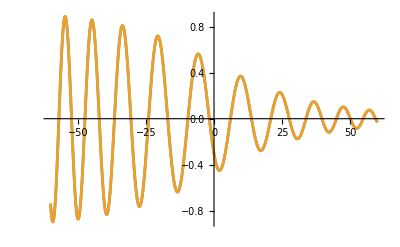

/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta01/omega02/V2/prob_base1

```mathematica
Plot[{Im[Exp[-2 alphaZ[t]]],-Im[(Exp[-alphaZ[t]] alphaMenos[t] alphaMas[t] + Exp[alphaZ[t]])^2]}, {t, -60, 60}]
```

ENERGY LEVELS

```mathematica
Emas[T_]:= 1/2 Sqrt[Ω^2 +del[T]^2]
```

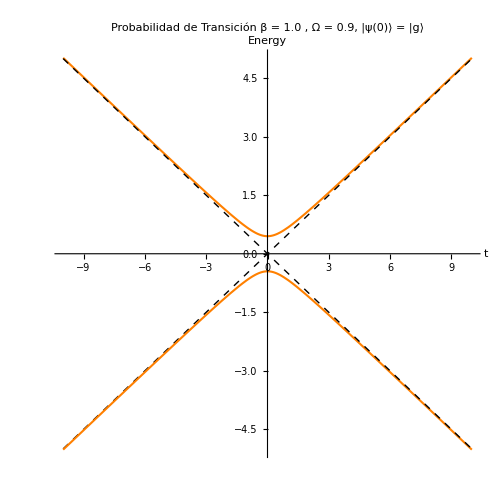

```mathematica
Plot[{Emas[t], 1/2 del[t],-Emas[t], -1/2 del[t]}, {t, -10, 10}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.003], Orange], Directive[Thickness[0.002], Dashed, Black],Directive[Thickness[0.003], Orange],Directive[Thickness[0.002], Dashed, Black]},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["Energy",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,PlotLabel->Style["Probabilidad de Transición  β = 1.0 , Ω = 0.9, |ψ(0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/escalado/lineal/interaccion_debil/beta1/omega09/niveles_energia",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/escalado/lineal/interaccion_debil/beta1/omega09/niveles_energia

## Espectro EW estado base

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S1[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
del[T_]:= T β^2;
```

```mathematica
IN3[ω_, T_]:= Δ/(4 Ωr)(I*NIntegrate[Exp[(Γ-I (ω-ν))t]Sin[Ωr t],{t,0,T}]*NIntegrate[Exp[(Γ+I (ω-ν))t],{t,0,T}]- I*NIntegrate[Exp[(Γ+I (ω-ν))t]Sin[Ωr t],{t,0,T}]*NIntegrate[Exp[(Γ-I (ω-ν))t],{t,0,T}])
```

```mathematica
LN1[ω_, T_]:= 1/16 Abs[(Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I (ω-ν-Ωr))-(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I (ω-ν+Ωr))]^2
```

```mathematica
LN2[ω_,T_]:= 1/16 Abs[(2 (Exp[(Γ-I (ω-ν))T]-1))/(Γ-I (ω-ν))-(Exp[(Γ- I (ω-ν-Ωr))T]-1)/(Γ- I (ω-ν-Ωr))-(Exp[(Γ- I (ω-ν+Ωr))T]-1)/(Γ- I (ω-ν+Ωr))]^2
```

```mathematica
LN3[ω_, T_]:= 1/4 Re[((Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I(ω-ν-Ωr))-(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I(ω-ν+Ωr)))((Exp[(Γ+I(ω-ν))T]-1)/(Γ+ I (ω-ν)))]
```

```mathematica
LN4[ω_, T_]:= Δ/(8 Ωr)(Abs[(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I(ω-ν+Ωr))]^2-Abs[(Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I(ω-ν-Ωr))]^2)
```

```mathematica
LN4[ω_, T_]:= Δ/(8 Ωr)(Abs[(Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I(ω-ν-Ωr))]^2-Abs[(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I(ω-ν+Ωr))]^2)
```

```mathematica
SBasNum[ω_, T_]:= 2Γ Exp[-2 Γ T]((Ω/Ωr)^2)(LN1[ω,T] + LN2[ω,T] + Re[IN3[ω, T]]+LN4[ω,T])
```

```mathematica
L1[ω_, T_]:= 1/16 Abs[(Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I (ω-ν-Ωr))(1-Δ/Ωr)^2+(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I (ω-ν+Ωr))(1+Δ/Ωr)^2+ 2 (1-Δ^2/Ωr^2)(Exp[(Γ-I(ω-ν))T]-1)/(Γ- I (ω-ν))]^2
```

```mathematica
II1[ω_, T_]:= 1/16 Abs[(Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I (ω-ν-Ωr))-(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I (ω-ν+Ωr))]^2
```

```mathematica
II2[ω_,T_]:= 1/16((Δ/Ωr)^2)Abs[(2 (Exp[(Γ-I (ω-ν))T]-1))/(Γ-I (ω-ν))-(Exp[(Γ- I (ω-ν-Ωr))T]-1)/(Γ- I (ω-ν-Ωr))-(Exp[(Γ- I (ω-ν+Ωr))T]-1)/(Γ- I (ω-ν+Ωr))]^2
```

```mathematica
II3[ω_, T_]:= (1Δ)/(4 Ωr)Re[((Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I(ω-ν-Ωr))-(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I(ω-ν+Ωr)))((Exp[(Γ+I(ω-ν))T]-1)/(Γ+ I (ω-ν)))]
```

```mathematica
II4[ω_, T_]:= Δ/(8Ωr)(Abs[(Exp[(Γ-I(ω-ν+Ωr))T]-1)/(Γ-I(ω-ν+Ωr))]^2-Abs[(Exp[(Γ-I(ω-ν-Ωr))T]-1)/(Γ-I(ω-ν-Ωr))]^2)
```

```mathematica
L2[ω_, T_]:= (II1[ω,T] + II2[ω,T] +II3[ω,T]+ II4[ω,T])(Ω/Ωr)^2
```

```mathematica
SExcNum[ω_, T_]:= 2Γ Exp[-2 Γ T](L1[ω, T]+L2[ω, T])
```

```mathematica
Γ = 0.1;ν=0.0;T = -10;T0=-140;Ωr = Sqrt[(T*β^2)^2 + Ω^2 ]; Δ=-T*β^2;
```

```mathematica
ListLinePlot[ParallelTable[{ω,S1[Γ,ω,T,T0]},{ω,-2.2,2.2,0.015}],PlotRange->{-0.1,9.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],PlotLegends->"t=-10",
GridLines->{{{ν,Directive[Thickness[0.003],Red]},{ν-Ωr,Directive[Thickness[0.003],Red]},{ ν+Ωr,Directive[Thickness[0.003],Red]}},None}, PlotLabel->Style["Espectro Fisico EW   |ψ(0)⟩ = |g⟩ \n β = 1.0, Ω = 0.9, Γ = 0.1, t_0 = -240", 16, FontFamily->"Times New Roman", Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00010232-0.0000621252 ⅈ and 2.48829×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000635146+0.0000569865 ⅈ and 2.2799×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000328575-0.0000833538 ⅈ and 2.52886×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000947102-2.08267×10^-6 ⅈ and 2.47085×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000326699+0.0000956458 ⅈ and 2.39797×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000849851-0.000068445 ⅈ and 2.40607×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000111218-0.0000467841 ⅈ and 2.52662×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000466463+0.0000902835 ⅈ and 2.38434×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000744784-0.0000807202 ⅈ and 2.39877×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000020279-0.0000876414 ⅈ and 2.53601×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000944191+0.0000119543 ⅈ and 2.46976×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000071489+0.0000471446 ⅈ and 2.25312×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000117832-0.0000301749 ⅈ and 2.48436×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000622085-0.0000913939 ⅈ and 2.38632×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000597551+0.0000828888 ⅈ and 2.40139×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000779469+0.000036196 ⅈ and 2.32355×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.15437×10^-6-0.0000900391 ⅈ and 2.53227×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000920567+0.0000258594 ⅈ and 2.46038×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000153385-4.38994×10^-7 ⅈ and 2.40384×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000026526+0.00013159 ⅈ and 2.35301×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000385215-0.000178011 ⅈ and 2.41665×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000206747+0.0000988181 ⅈ and 2.41325×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_debil/beta01/omega02/t=28",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_debil/beta01/omega02/t=28

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2}, {t, -200, 200}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->Thickness[0.003],PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->440,
PlotLabel->Style["Probabilidades de Transición, t = 180", 18, FontFamily->"Times New Roman", Black], GridLines->{{{T,Directive[Thickness[0.003],Green]}},None}]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta02/omega08/comp_mollow/t=150",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta02/omega08/comp_mollow/t=150

```mathematica
P2=ListLinePlot[ParallelTable[{ω,SExcNum[ω,Abs[T0]+T]},{ω,-1.2,6.8,0.015}],PlotRange-> {-0.1, 20.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Red,Thickness[0.004], Opacity[0.3]],FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ)",22,FontFamily->"Times New Roman",Gray]},ImageSize->500];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

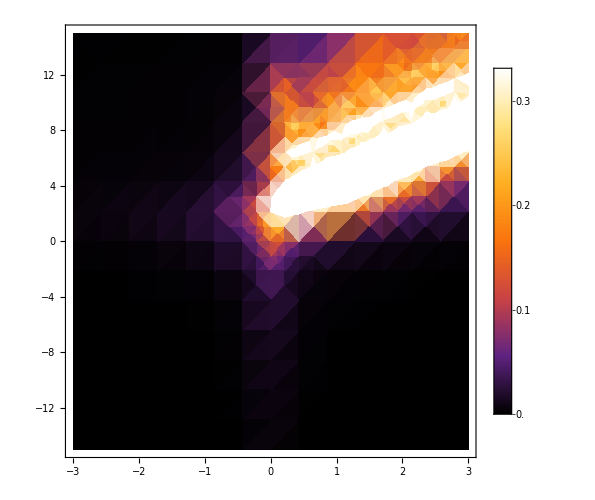

```mathematica
DensityPlot[S1[0.1,ω,T,-240],{ω,-3.0,3.0},{T,-15,15},ColorFunction->"SunsetColors",PlotLegends->Automatic, ImageSize->500]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta01/omega02/V2/density",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta01/omega02/V2/density

### Comparación caso limite sin interacción

```mathematica
EWLinear[Γ_,β_,ω_,T_]:=(π Γ)/(2 β^2)Exp[-2 Γ (T-ω /(2β^2))]Abs[Erfc[(I^(1/2))(Γ-I (ω-2T β^2))/(2β)]]^2
```

```mathematica
Γ = 0.1;ν=0.0;T = 0;T0=-220;Ωr = Sqrt[(T*β^2)^2 + Ω^2 ]; Δ=-T*β^2;
```

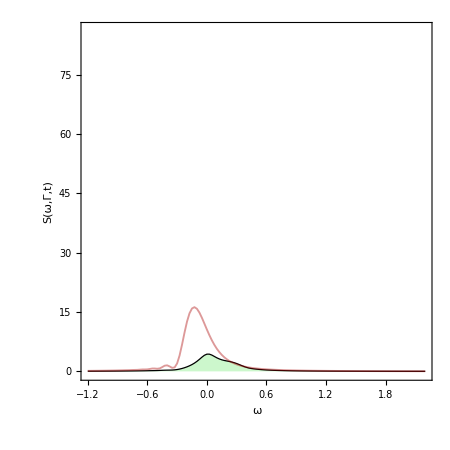

```mathematica
G1 =Show[ListLinePlot[ParallelTable[{ω,0+S1[Γ,ω,T,T0]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=0",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,0+EWLinear[Γ,β/Sqrt[2],ω,0]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

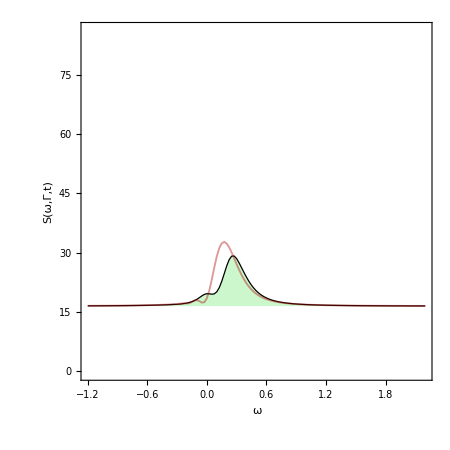

```mathematica
G2 =Show[ListLinePlot[ParallelTable[{ω,16.5+S1[0.1,ω,30,T0]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Filling->16.5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=30",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,16.5+EWLinear[Γ,β/Sqrt[2],ω,30]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

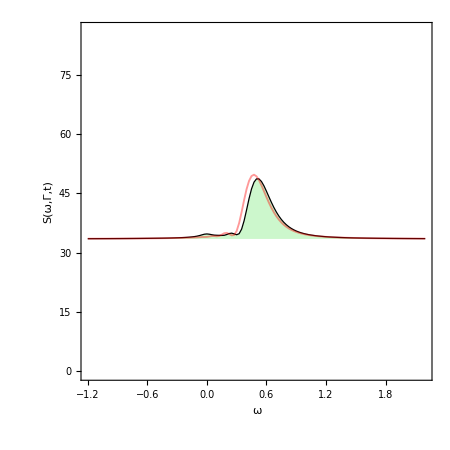

```mathematica
G3=Show[ListLinePlot[ParallelTable[{ω,33.5+S1[Γ,ω,60,T0]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Filling->33.5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=60",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,33.5+EWLinear[Γ,β/Sqrt[2],ω,60]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Red,Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

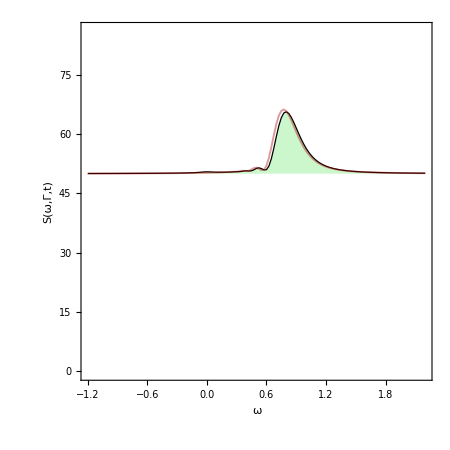

```mathematica
G4=Show[ListLinePlot[ParallelTable[{ω,50+S1[Γ,ω,90,T0]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Filling->50,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=90",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,50+EWLinear[Γ,β/Sqrt[2],ω,90]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

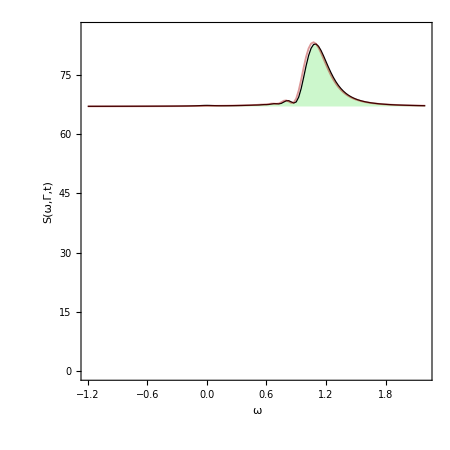

```mathematica
G5=Show[ListLinePlot[ParallelTable[{ω,67+S1[Γ,ω,120,T0]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Filling->67,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=120",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,67+EWLinear[Γ,β/Sqrt[2],ω,120]},{ω,-1.2,2.2,0.025}],PlotRange->{-0.5,86.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

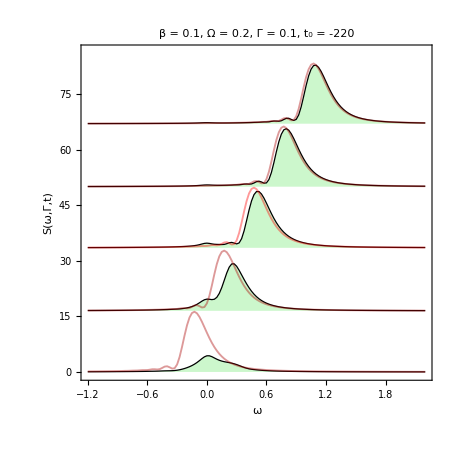

```mathematica
Show[{G5,G4,G3,G2,G1}, PlotLabel-> Style["β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -220", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/limite_lineal3",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/limite_lineal3

## Espectro EW estado excitado

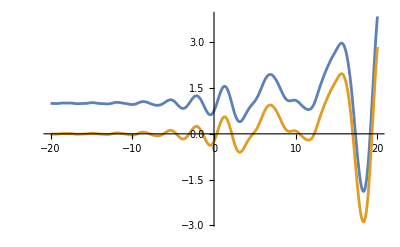

```mathematica
Plot[{Im[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]]+1, -Im[Exp[(Γ+I ω)t](-alphaMas[t] - Exp[-2alphaZ[t]](alphaMas[t]^2)alphaMenos[t])]}, {t, -20, 20}]
```

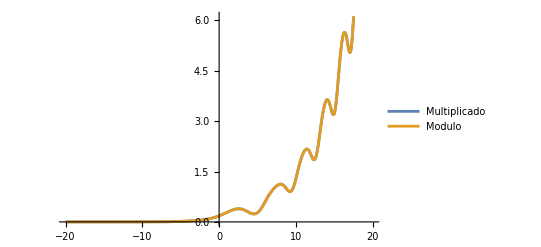

```mathematica
Plot[{Re[(Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t])(Exp[(Γ+I ω)t](-alphaMas[t] - Exp[-2alphaZ[t]]alphaMenos[t]alphaMas[t]^2))],Abs[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]]^2}, {t, -20, 20}, PlotLegends->{"Multiplicado", "Modulo"}]
```

```mathematica
L1[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
L2[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S2[Γ_,ω_,T_,T0_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T,T0]+L2[Γ,ω,T,T0])
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

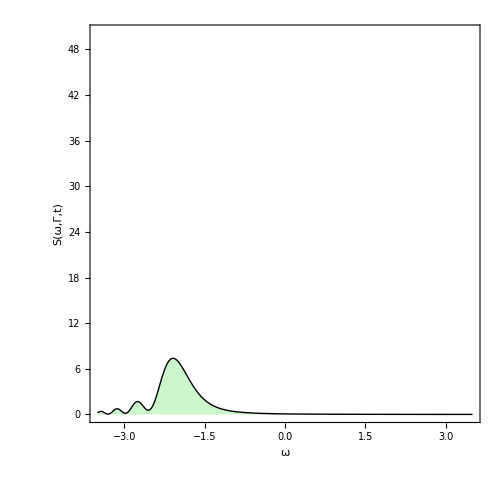

```mathematica
G1 =ListLinePlot[ParallelTable[{ω,S2[0.1,ω,-20,-200]},{ω,-3.5,3.5,0.025}],PlotRange->{-0.05,50.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/Screenshots/Lineal/b=01_0=025/zoom_omega_excitado2/t=52.png",G1,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/Screenshots/Lineal/b=01_0=025/zoom_omega_excitado2/t=52.png

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99384×10^-7+0.0000400718 ⅈ and 4.61231×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000237749-0.0000234867 ⅈ and 4.65487×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

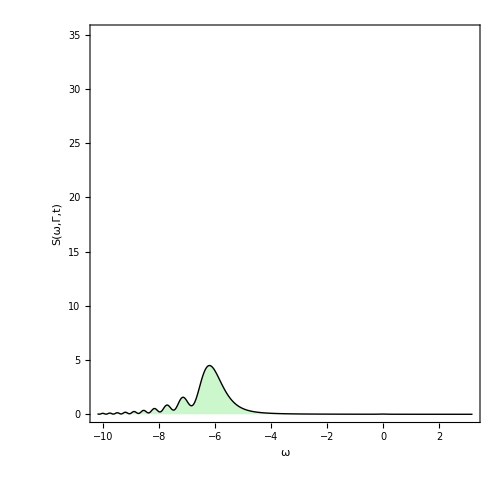

```mathematica
G2 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-30,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-30",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

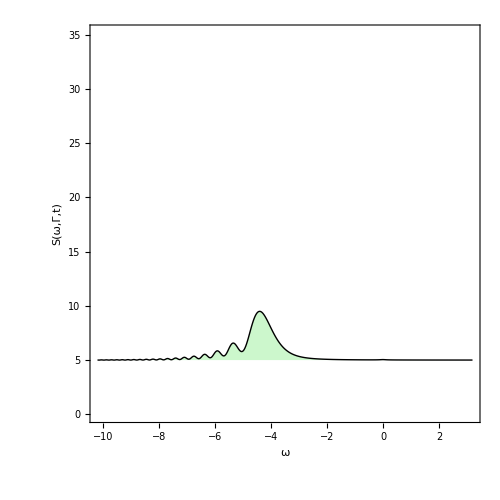

```mathematica
G3=ListLinePlot[ParallelTable[{ω,5+S2[0.1,ω,-20,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

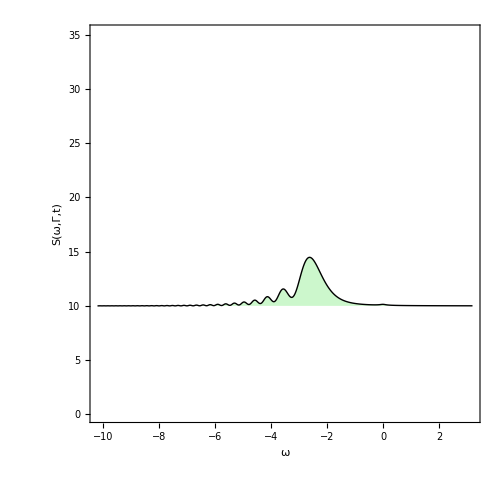

```mathematica
G4 =ListLinePlot[ParallelTable[{ω,10+S2[0.1,ω,-10,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-10",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

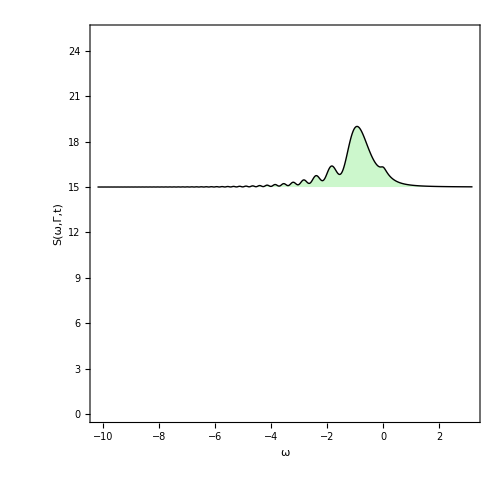

```mathematica
G5 =ListLinePlot[ParallelTable[{ω,15+S2[0.1,ω,0,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=0",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

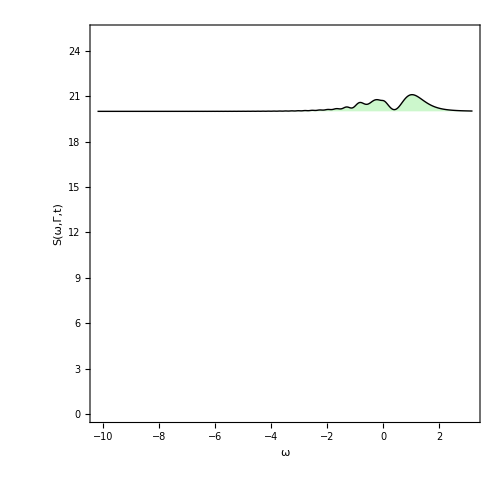

```mathematica
G6 =ListLinePlot[ParallelTable[{ω,20+S2[0.1,ω,10,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

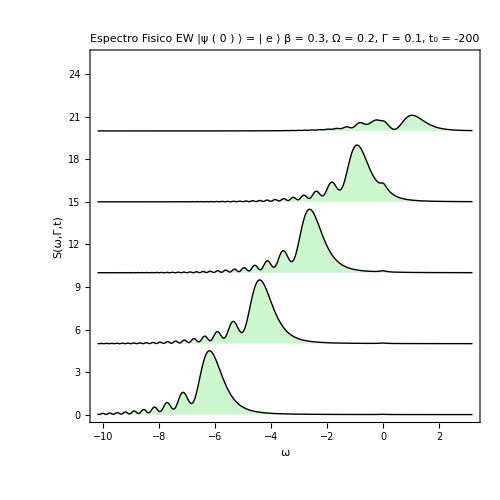

```mathematica
Show[G6,G5,G4,G3,G2, 
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | e ⟩ \n β = 0.3, Ω = 0.2, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

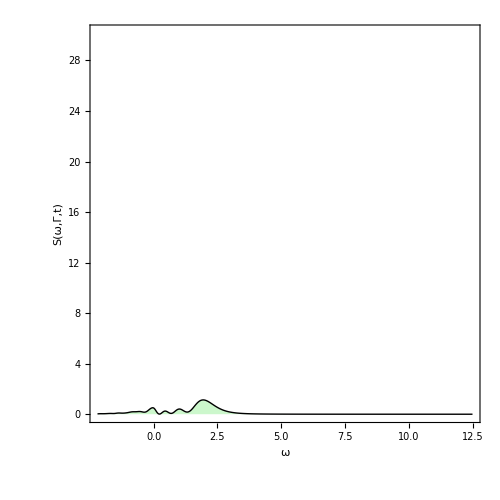

```mathematica
G9 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,15,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,30.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=15",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

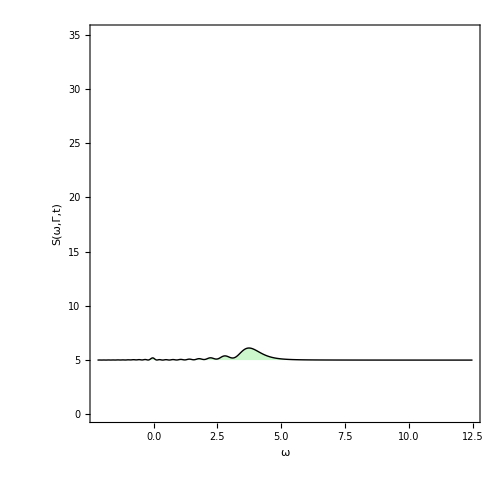

```mathematica
G10 =ListLinePlot[ParallelTable[{ω,5+S2[0.1,ω,25,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=25",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

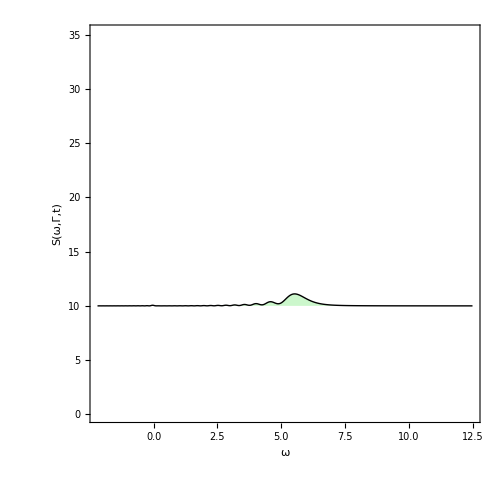

```mathematica
G11 = ListLinePlot[ParallelTable[{ω,10+S2[0.1,ω,35,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=35",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

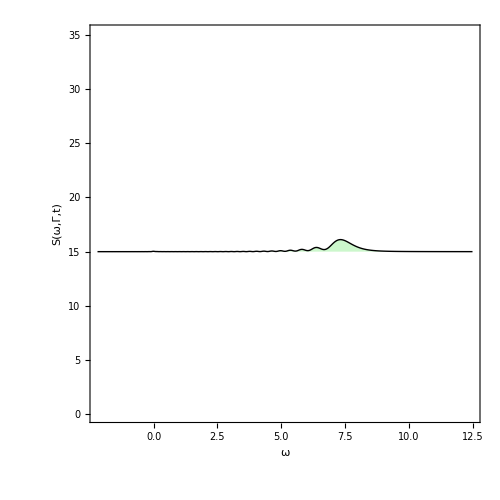

```mathematica
G12 = ListLinePlot[ParallelTable[{ω,15+S2[0.1,ω,45,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=45",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

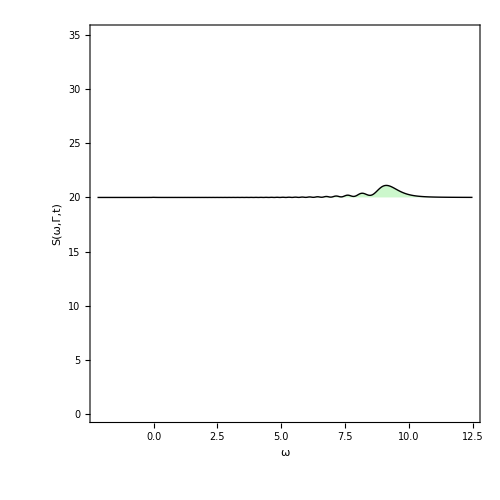

```mathematica
G13 = ListLinePlot[ParallelTable[{ω,20+S2[0.1,ω,55,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=55",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

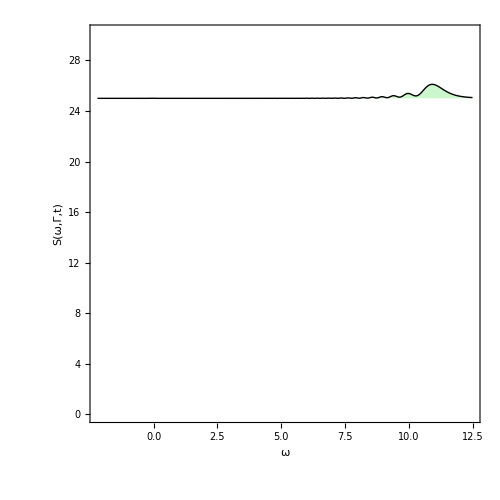

```mathematica
G14 = ListLinePlot[ParallelTable[{ω,25+S2[0.1,ω,65,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,30.2},Filling->25,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=65",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

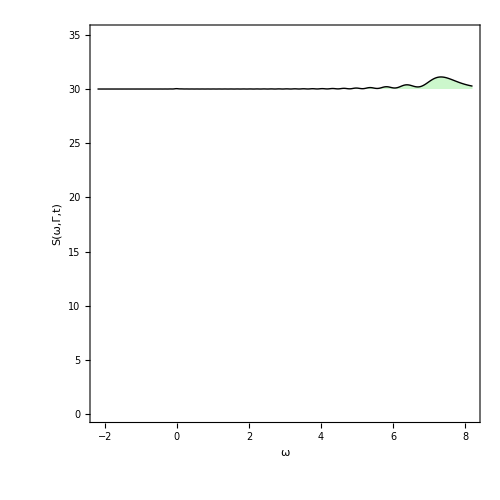

```mathematica
G15 = ListLinePlot[ParallelTable[{ω,30+S2[0.1,ω,45,-200]},{ω,-2.2,8.2,0.025}],PlotRange->{-0.05,35.2},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=45",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

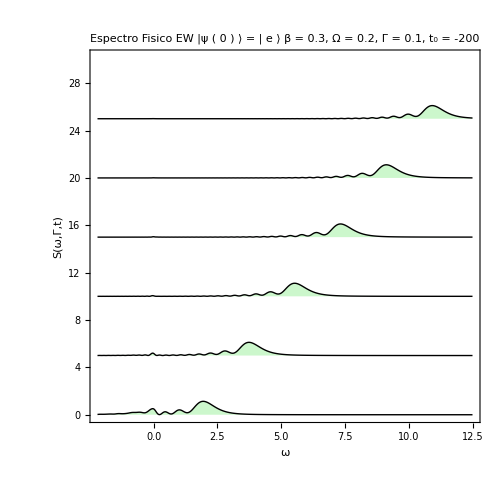

```mathematica
Show[G14,G13,G12,G11,G10,G9, 
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | e ⟩ \n β = 0.3, Ω = 0.2, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

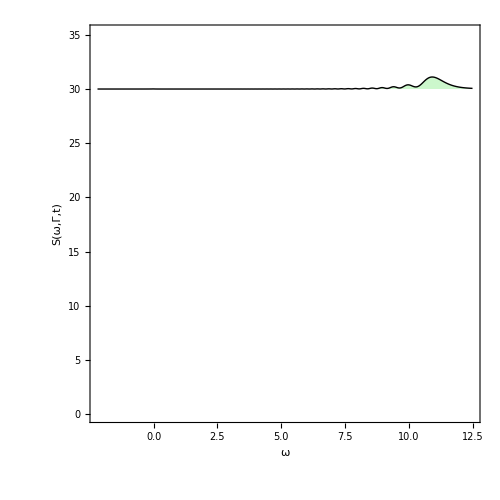

```mathematica
G16= ListLinePlot[ParallelTable[{ω,30+S2[0.1,ω,65,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=65",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```